```mathematica
$ImportFormats;
scatterdata=Import["C:\\Users\\shahn\\OneDrive\\Desktop\\Undergraduate project\\Ge Gm.csv"];
```

```mathematica
qvalues = scatterdata[[2;;12,1]];
```

```mathematica
(*Calculation for Subscript[μ, p] Subscript[G, E]/Subscript[G, M] graph*)
GeGmvalues = scatterdata[[2;;12,13]];
errors1= scatterdata[[2;;12,14]];
GeGmerror=  Table[Around[GeGmvalues[[i]],errors1[[i]]],{i,1,Length[GeGmvalues]}];
RatioGeGmerror= Transpose[{qvalues, GeGmerror}];
RatioGeGm = Transpose[{qvalues, GeGmvalues}];
```

```mathematica
(*fit function for Subscript[μ, p] Subscript[G, E]/Subscript[G, M] graph*)
fitGeGm=  Fit[RatioGeGm,{1,x,x^2,x^3},x];
```

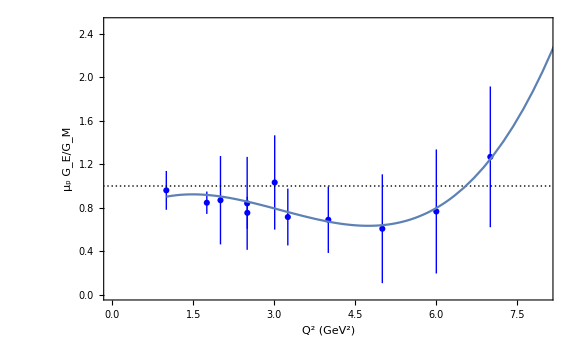

```mathematica
(*Graph for Subscript[μ, p] Subscript[G, E]/Subscript[G, M] vs Q^2*)
Show[ListPlot[RatioGeGmerror,PlotMarkers->Automatic,PlotStyle->Blue,PlotTheme-> "Monochrome"]/.RGBColor[__]:> RGBColor[0,0,1],Plot[fitGeGm,{x,1,10}] ,BaseStyle-> {FontFamily-> "Times New Roman"},Frame-> True,FrameLabel-> {"Q^2 (GeV^2)", "μ_p G_E/G_M"},PlotRange-> {{0,8},{0,2.5}}, GridLines-> {{},{1}}, ImageSize-> Large]
```

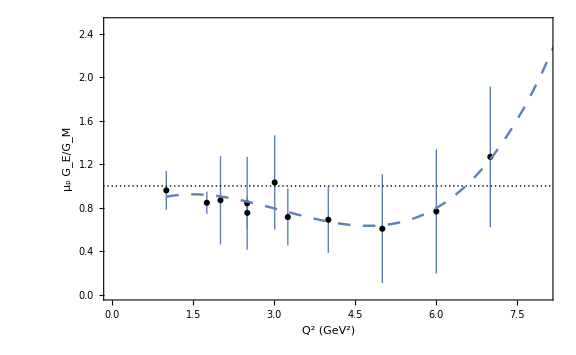

```mathematica
Show[ListPlot[RatioGeGmerror,PlotMarkers->Automatic,PlotStyle-> Automatic,PlotTheme-> "Monochrome"],Plot[fitGeGm,{x,1,10},PlotStyle-> {Thickness[.003],Dashing[Medium]}] ,LabelStyle->Directive [FontFamily-> "Times",FontSize->20],Frame-> True,FrameLabel-> {"Q^2 (GeV^2)", "μ_p G_E/G_M"},PlotRange-> {{0,8},{0,2.5}}, GridLines-> {{},{1}}, ImageSize-> Large]
```

```mathematica
(*Calculation for Subscript[G, E]/Subscript[G, D] graph*)
GeGdvalues = scatterdata[[2;;12,16]];
errors2= scatterdata[[2;;12,17]];
GeGderror=  Table[Around[GeGdvalues[[i]],errors2[[i]]],{i,1,Length[GeGdvalues]}];
RatioGeGderror= Transpose[{qvalues, GeGderror}];
RatioGeGd = Transpose[{qvalues, GeGdvalues}];
```

```mathematica
(*fit function for Subscript[G, E]/Subscript[G, D] graph*)
fitGeGd=  Fit[RatioGeGd,{1,x,x^2,x^3},x];
```

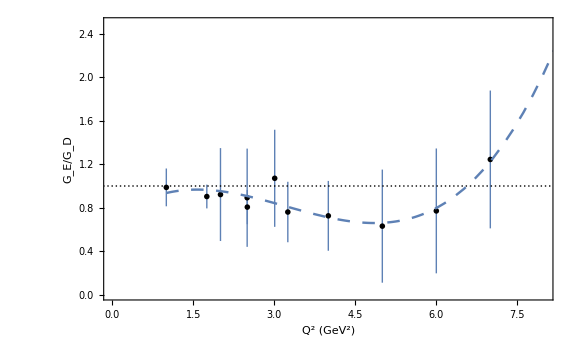

```mathematica
(*Graph for Subscript[G, E]/Subscript[G, D] vs Q^2*)
Show[ListPlot[RatioGeGderror, PlotTheme-> "Monochrome"],Plot[fitGeGd,{x,1,10},PlotStyle-> {Thickness[.003],Dashing[Medium]}] ,LabelStyle->Directive [FontFamily-> "Times",FontSize->20],Frame-> True,FrameLabel-> {"Q^2 (GeV^2)", "G_E/G_D"},PlotRange-> {{0,8},{0,2.5}}, GridLines-> {{},{1}}, ImageSize-> Large]
```

```mathematica
(*Calculation for Subscript[G, M]/Subscript[μ, p] Subscript[G, D] graph*)
GmGdvalues = scatterdata[[2;;12,18]];
errors3= scatterdata[[2;;12,19]];
GmGderror=  Table[Around[GmGdvalues[[i]],errors3[[i]]],{i,1,Length[GmGdvalues]}];
RatioGmGderror= Transpose[{qvalues, GmGderror}];
RatioGmGd = Transpose[{qvalues, GmGdvalues}];
```

```mathematica
(*fit function for Subscript[G, M]/Subscript[μ, p] Subscript[G, D] graph*)
fitGmGd=  Fit[RatioGmGd,{1,x,x^2},x];
```

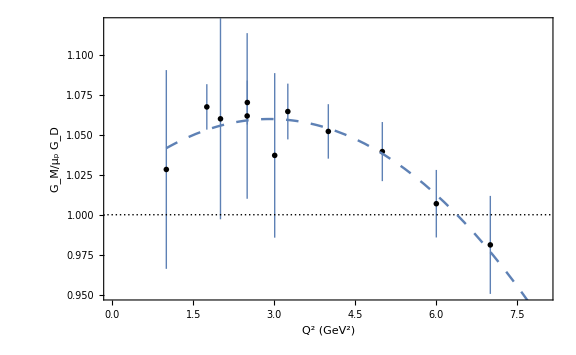

```mathematica
(*Graph for Subscript[G, M]/Subscript[μ, p] Subscript[G, D] vs Q^2*)
Show[ListPlot[RatioGmGderror, PlotTheme-> "Monochrome"],Plot[fitGmGd,{x,1,10},PlotStyle-> {Thickness[.003],Dashing[Medium]}] ,LabelStyle->Directive [FontFamily-> "Times",FontSize->20],Frame-> True,FrameLabel-> {"Q^2 (GeV^2)", "G_M/μ_p G_D"},PlotRange-> {{0,8},{0.95,1.12}}, GridLines-> {{},{1}}, ImageSize-> Large]
```